This is a modularized version of Ina’s screening code

```mathematica
"We want to make sure we match on to this - the plot from the original version of the code."
```

We want to make sure we match on to this - the plot from the original version of the code.

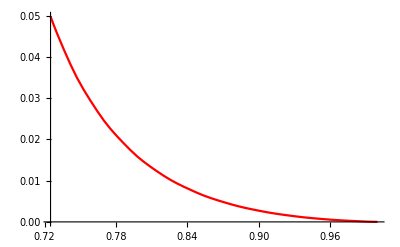

```mathematica
f=Interpolation[phiList];
testCurrent=Plot[f[x],{x,phiList[[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]
```

#### MB Distribution Case

```mathematica
N@vInfList 
"What are the units here? Is it relative to vesc? or v0?"
```

vInfList

What are the units here? Is it relative to vesc? or v0?

```mathematica
derivF[i_,RMax_,r_,phi_?NumericQ,n_,vInfList_,RMaxList_,MBfactor_]:=
(*Used to find a good endpoint for solving the F[phi]=0 equation (there can be a superfluous root at higher phi)*)Re[N[(-3 ⅇ^(-3phi)/2-3 ⅇ^(3phi/2)/2)/n+((MBfactor/(2*√(vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]]))vInfList[[i]]))),20]];(*CHANGED*)

complexF[i_,RMax_,r_,vInfList_,RMaxList_]:=
(*find where the function F[phi] (where we are solving F[phi]=0 to find phi) goes complex, which will cause the root finding protocol to not work well*)
N[RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])-vInfList[[i]]^2,50];

rootF[i_,RMax_,r_,phi_?NumericQ,n_,vInfList_,RMaxList_,MBfactor_]:=

Re[N[(ⅇ^(-3phi/2)-ⅇ^(3phi/2))/n+MBfactor/vInfList[[i]] Sqrt[vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])],50]];(*CHANGED*)
```

```mathematica
Clear[GetScreenedϕ]
GetScreenedϕ[phiEarth_:0.05,vInfList_:PowerRange[1/20,4,1+2/10](*,pointNumber_:100*)]:=Module[{MBNorm,MBfactor,pointNumber=100,phiList={{1,0}},RMaxList={{1,0}},minPoint =SetPrecision[ 0.5,20],scanPoints,earthFlag,zoomFlag,phiListWorking,delNum,zoomCount,phiMin,phiMax,res,successplot,phiNew,phiFunc,ckplot,insertPoints,f},

(*pointNumber=100;*)(*keep pointnumber low for fast run times, ~100 works well*)

MBNorm=SetPrecision[Sum[vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2],{i,1,Length[vInfList]}],20];
MBfactor[i_]:=SetPrecision[ vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2]/MBNorm,20];

(* start of recursion to scan over different r's to find escape potential *)
(*phiList={{1,0}};*)
(*RMaxList={{1,0}};*)
(*minPoint =SetPrecision[ 0.5,20];*)(*CHANGED*)
Clear[scanPoints];
scanPoints=SetPrecision[Table[1-i(1-minPoint)/pointNumber,{i,pointNumber}],20];
earthFlag=False (*triggers True when escape potential matches Earth potential*);
zoomFlag=False (*triggers True when the recursion zooms in to finer value of the radius*);
(*recursion over different values of v_inf*)
Do[
phiListWorking = {};
delNum=0;
zoomCount=0;
If[earthFlag,Break[]];
If[zoomFlag,Break[]];
Print[j];
(*recursion over different values of r*);
Do[
If[zoomCount>12,zoomFlag=True;Print["You've zoomed in more than 12 times, problem?"];
Break[]];

phiMin=Max[Table[complexF[l,RMaxList[[l,1]],scanPoints[[k]],vInfList,RMaxList],{l,j}]]+10^(-15);
Do[If[Sqrt[vInfList[[l]]^2+phiMin-RMaxList[[l,1]]^2/scanPoints[[k]]^2(vInfList[[l]]^2+RMaxList[[l,2]])]<=10^-8,
phiMin+=10^-12],
{l,j}];

phiMax=phi/.FindRoot[Sum[derivF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],{phi,phiMin,0.1},Method->"Brent"];

res=Check[FindRoot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],
{phi,phiMin-10^(-12),phiMax},
Method->"Brent",WorkingPrecision->20],$Failed[Evaluate@$MessageList],
FindRoot::bbrac];


If[
FreeQ[res,$Failed](*check whether FindRoot was succesful*),
successplot=Plot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],{phi,phiMin-10^(-12),phiMax}];(*ADDED*)
phiNew=phi/.res;
If[phiNew>phiEarth,(*CHANGED*)
earthFlag=True;phiList=Join[phiList,phiListWorking];Print["Reached Earth phi"];
Break[]];

(*make updated potential function so far*);
AppendTo[phiListWorking,{scanPoints[[k]],phiNew}];
phiFunc=Interpolation[Join[phiList,phiListWorking]];
delNum+=1;

(*check if we have hit RMax(v_inf)*);
If[phiFunc'[scanPoints[[k]]]*scanPoints[[k]]+2phiFunc[scanPoints[[k]]]+2(vInfList[[j+1]])^2<=0,AppendTo[RMaxList,{scanPoints[[k]],phiNew}];
phiList=Join[phiList,phiListWorking];
scanPoints=Drop[scanPoints,delNum];
pointNumber-=k;
Return[phiList[[-1]]];];,

(*if FindRoot was not succesful, go back a step in r and insert extra points to "fine-grain" your scan over r*)
Print["Zooming In"];
ckplot=Plot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j,vInfList,RMaxList,MBfactor[i]],{i,1,j}],{phi,phiMin-10^(-12),phiMax}];(*ADDED*)
zoomCount+=1;
(*pick extra points to insert*);
If[k==1,insertPoints=Table[RMaxList[[j,1]]-(RMaxList[[j,1]]-scanPoints[[k]])/10 p,{p,0,9}],insertPoints=Table[scanPoints[[k-1]]+(scanPoints[[k]]-scanPoints[[k-1]])/10 p,{p,0,9}]];

scanPoints=Join[scanPoints[[1;;k-1]],insertPoints,scanPoints[[k;;]]];
pointNumber+=10;
delNum+=1
],

{k,10000}],
{j,1,Length[vInfList]-1}];


f=Interpolation[phiList];

<|"ϕ(r)"->f,"phiList"->phiList|>
]
```

```mathematica
ϕtest=GetScreenedϕ[0.06,PowerRange[1/20,4,1+2/10]];
```

1

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

Zooming In

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

2

3

4

5

6

7

8

9

10

11

12

13

14

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

ReplaceAll::reps: {FindRoot[∑_(i=1)^j derivF[i,RMaxList$35916⟦i,1⟧,scanPoints$35916⟦k⟧,phi,j,{1/20,3/50,9/125,54/625,324/3125,1944/15625,11664/78125,69984/390625,419904/1953125,2519424/9765625,«15»},RMaxList$35916,MBfactor$35916[i]],{phi,phiMin$35916,0.1},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∑_(i=1)^j derivF[i,RMaxList$35916⟦i,1⟧,scanPoints$35916⟦k⟧,phi,j,{1/20,3/50,9/125,54/625,324/3125,1944/15625,11664/78125,69984/390625,419904/1953125,2519424/9765625,«15»},RMaxList$35916,MBfactor$35916[i]],{phi,phiMin$35916,0.1},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NSum::nsnum: Summand (or its derivative) derivF[i,RMaxList$35916⟦i,1⟧,scanPoints$35916⟦k⟧,phi,j,{1/20,3/50,9/125,54/625,324/3125,1944/15625,11664/78125,69984/390625,419904/1953125,2519424/9765625,«15»},RMaxList$35916,MBfactor$35916[i]] is not numerical at point i = 1.

General::stop: Further output of NSum::nsnum will be suppressed during this calculation.

FindRoot::srect: Value phi/.FindRoot[NSum[derivF[i,RMaxList$35916⟦i,1⟧,scanPoints$35916⟦k⟧,phi,j,{1/20,3/50,9/125,54/625,324/3125,1944/15625,11664/78125,69984/390625,419904/1953125,2519424/9765625,«15»},RMaxList$35916,MBfactor$35916[i]],{i,1,j},WorkingPrecision→28.6419,AccuracyGoal→∞,PrecisionGoal→18.6419],{phi,phiMin$35916,0.1},Method→Brent] in search specification {phi,phiMin$35916-1/10^12,phiMax$35916} is not a number or array of numbers.

Zooming In

Plot::plln: Limiting value phi/.FindRoot[∑_(i=1)^j derivF[i,RMaxList$35916⟦i,1⟧,scanPoints$35916⟦k⟧,phi,j,{1/20,3/50,9/125,54/625,324/3125,1944/15625,11664/78125,69984/390625,419904/1953125,2519424/9765625,«15»},RMaxList$35916,MBfactor$35916[i]],{phi,phiMin$35916,0.1},Method→Brent] in {phi,0.0640553681547027357,phi/.FindRoot[∑_(i=1)^j derivF[i,RMaxList$35916⟦i,1⟧,scanPoints$35916⟦k⟧,phi,j,{1/20,3/50,9/125,54/625,324/3125,1944/15625,11664/78125,69984/390625,419904/1953125,2519424/9765625,«15»},RMaxList$35916,MBfactor$35916[i]],{phi,phiMin$35916,0.1},Method→Brent]} is not a machine-sized real number.

Reached Earth phi

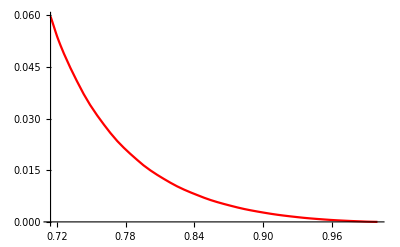

```mathematica
testCurrent=Plot[ϕtest["ϕ(r)"][x],{x,ϕtest["phiList"][[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]
```